# ProbeParticle position view

This notebook is basically doing the same thing plot_results.py -- pos but in Mathematica Style.
Done loong time ago

```mathematica
atomicprop=Import["~/Documents/atomic_prop.dat","Table"];
path="~/Desktop/Tarkil/molekuly/PTCDA-0.2/";
(*path="~/Desktop/";*)
xsfin1=Import[path<>"OutX.xsf","Table"];
xsfin2=Import[path<>"OutY.xsf","Table"];
const=17
lvs1=xsfin1[[{const+2,const+3,const+4},All]]
n=xsfin1[[const+0,{1,2,3}]]
d={1/(n[[1]]-1)*Norm[lvs1[[1]]],1/(n[[2]]-1)*Norm[lvs1[[2]]],1/(n[[3]]-1)*Norm[lvs1[[3]]]}
```

17

{{25.,0.,0.},{0.,19.,0.},{0.,0.,1.6}}

{251,191,16}

{0.1,0.1,0.106667}

```mathematica
n[[3]]=70;(*just for fast*)
```

```mathematica
l=(*10*)5(*1*);
XY2=Array[Null,{n[[3]],((n[[2]]-1)/l+1)*((n[[1]]-1)/l+1)}];
Dimensions[XY2]
```

{16,1989}

```mathematica
a=1;b=1;
For[i=1,i<=n[[3]],i++,
{For[j=1,j≤n[[2]],j++,
{For[k=1,k≤n[[1]],k++,
{If[Mod[j-1,l]==0&&Mod[k-1,l]==0,{XY2[[i,Mod[b-1,Dimensions[XY2][[2]]]+1]]={(k-1)*d[[1]]+xsfin1[[const+a+4,1]],(j-1)*d[[2]]+xsfin2[[const+a+4,1]]},b=b+1}],a=a+1}]
}],Print[i]}]
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

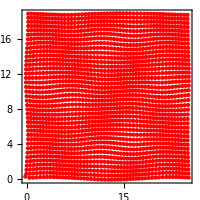
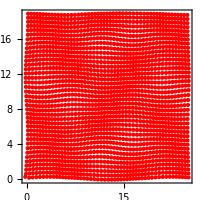
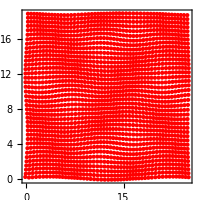
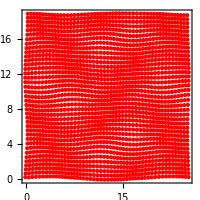
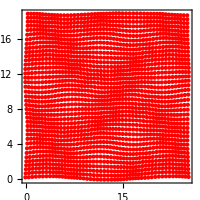
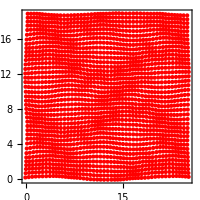
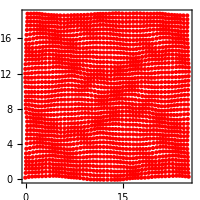
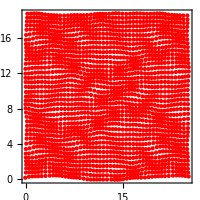

```mathematica
outXY=Table[Graphics[{Red,PointSize[Tiny(*Small*)],Point[XY2[[i]]]}(*,PlotRange->{{-0.1+stp[[1]],stp+Norm[lvs1[[1]]]+0.1},{-0.1+stp[[2]],stp+Norm[lvs1[[2]]]+0.1}}*),ImageSize->200,Frame->True,FrameLabel->{None,None,Text[Style["d="<>ToString[-(i-1)*d[[3]]],FontSize->20]],None}],{i,1,1n[[3]]}(*{i,1,70(*{4,8,11,14}*)}*)]
```

```mathematica
Export[path<>"outXY-martin-tiny-twice.png",TableForm[outXY,TableDirections->Row],Background->White]
```

~/Desktop/outXY-martin-tiny-twice.png

```mathematica
Export["~/Desktop/outXY_4.png",TableForm[outXY,TableDirections->Row],Background->White]
```

~/Desktop/outXY_4.png

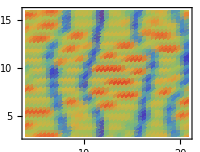
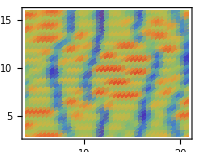
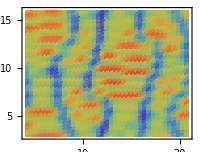
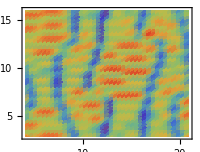
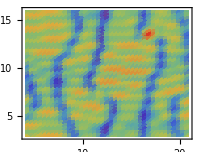
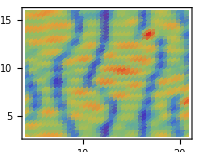
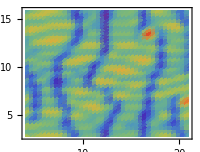
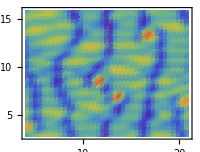

```mathematica
outDens=Table[SmoothDensityHistogram[XY2[[i]],.3,PlotRange->{{-0.1+stp[[1]],stp+Norm[lvs1[[1]]]+0.1},{-0.1+stp[[2]],stp+Norm[lvs1[[2]]]+0.1}},ImageSize->200,Frame->True,ColorFunction->"Rainbow",AspectRatio->Norm[lvs1[[2]]]/Norm[lvs1[[1]]],FrameLabel->{None,None,Text[Style["d="<>ToString[-(i-1)*d[[3]]],FontSize->20]],None}],(*{i,1,1n[[3]]}*){i,4,18}]
```

```mathematica
Export[path<>"outDens.png",TableForm[outDens,TableDirections->Row],Background->White]
```

~/Desktop/Tarkil/molekuly/PTCDA_ruslan/outDens.png

```mathematica
stp ={0,0,0};
```

```mathematica
XY=Array[Null,{n[[3]],n[[2]]*n[[1]]}];Dimensions[XY]
```

{21,47941}

```mathematica
a=1;For[i=1,i<=n[[3]],i++,
{For[j=1,j≤n[[2]],j++,
{For[k=1,k≤n[[1]],k++,
{XY[[i,Mod[a-1,n[[2]]*n[[1]]]+1]]={(k-1)*d[[1]]+xsfin1[[const+a+4,1]],(j-1)*d[[2]]+xsfin2[[const+a+4,1]]},a=a+1}]
}],Print[i]}]
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

```mathematica
outXY=Table[Graphics[{PointSize[Tiny],Point[XY[[i]]]}(*,PlotRange->{{-0.1+stp[[1]],stp+Norm[lvs1[[1]]]+0.1},{-0.1+stp[[2]],stp+Norm[lvs1[[2]]]+0.1}}*),ImageSize->800,Frame->True,FrameLabel->{None,None,Text[Style["d="<>ToString[-(i-1)*d[[3]]],FontSize->20]],None}],(*{i,1,1n[[3]]}*){i,4,18}]
```

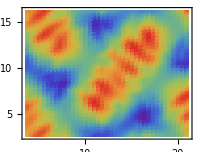
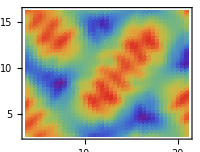
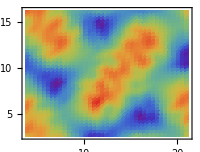
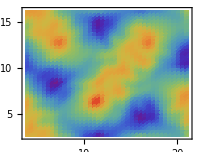
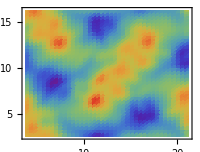
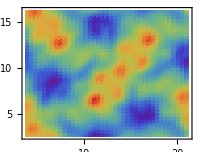
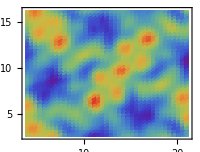
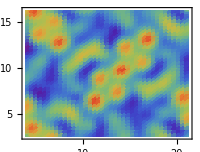

```mathematica
outDens=Table[SmoothDensityHistogram[XY[[i]],.4,PlotRange->{{-0.1+stp[[1]],stp+Norm[lvs1[[1]]]+0.1},{-0.1+stp[[2]],stp+Norm[lvs1[[2]]]+0.1}},ImageSize->200,Frame->True,ColorFunction->"Rainbow",AspectRatio->Norm[lvs1[[2]]]/Norm[lvs1[[1]]],FrameLabel->{None,None,Text[Style["d="<>ToString[-(i-1)*d[[3]]],FontSize->20]],None}],(*{i,1,1n[[3]]}*){i,4,18}]
```